```mathematica
dx1=0;
dx2=0;
dx3=0;

ds1=0;
ds2=0;
ds3=0;



X[1]=-1/2;
X[2]=1;
X[3]=-1/2;
X[4]=1/2;
X[5]=-1;
X[6]=1/2;

Y[1]=Sqrt[3]/2;
Y[2]=0;
Y[3]=-Sqrt[3]/2;
Y[4]=Sqrt[3]/2;
Y[5]=0;
Y[6]=-Sqrt[3]/2;



Z[1]=0;
Z[2]=0;
Z[3]=0;
Z[4]=0;
Z[5]=0;
Z[6]=0;

For[i=1,i≤6,i++,S[i]=Sqrt[X[i]^2+Y[i]^2+Z[i]^2]];
For[i=1,i≤6,i++,VN[i]={X[i],Y[i],Z[i]}/S[i]];
For[i=1,i≤6,i++,VN1[i]={-Y[i],X[i],0}/Sqrt[X[i]^2+Y[i]^2]];
For[i=1,i≤6,i++,VN2[i]=Cross[VN[i],VN1[i]]];
Clear[S1,S2,kx,ky,LZ]
NSS[1]=-S[1] VN[1];
NSS[2]=-S[2]VN[2];
NSS[3]=-2S[3]VN[3];
NSS[4]=-2S[4]VN[4];
NSS[5]=-S[5]VN[5];
NSS[6]=-S[6]VN[6];

NDS[1]=S1[2]VN1[2]+S1[3]VN1[3]+S2[2]VN2[2]+S2[3]VN2[3];
NDS[2]=S1[1]VN1[1]+S1[3]VN1[3]+S2[3]VN2[3];
NDS[3]=S1[1]VN1[1]+S1[2]VN1[2]+S1[4]VN1[4]+S2[2]VN2[2];
NDS[4]=S1[3]VN1[3]+S1[5]VN1[5]+S1[6]VN1[6]+S2[3]VN2[3]+S2[5]VN2[5]+S2[6]VN2[6];
NDS[5]=S1[4]VN1[4]+S1[6]VN1[6]+S2[6]VN2[6];
NDS[6]=S1[4]VN1[4]+S1[5]VN1[5]+S2[5]VN2[5];

DTS1[1]=-VN1[1].(LZ[1]S[1]Cross[VN2[1],VN[1]])/ii;
DTS1[4]=-VN1[4].(LZ[4]S[4]Cross[VN2[4],VN[4]])/ii;

DTS1[2]=VN1[2].(S[2]Cross[VN[2],NDS[2]]+S2[2]Cross[VN2[2],NSS[2]]+S1[2]Cross[VN1[2],NSS[2]]);
DTS1[3]=VN1[3].(S[3]Cross[VN[3],NDS[3]]+S2[3]Cross[VN2[3],NSS[3]]+S1[3]Cross[VN1[3],NSS[3]]);
DTS1[5]=VN1[5].(S[5]Cross[VN[5],NDS[5]]+S2[5]Cross[VN2[5],NSS[5]]+S1[5]Cross[VN1[5],NSS[5]]);
DTS1[6]=VN1[6].(S[6]Cross[VN[6],NDS[6]]+S2[6]Cross[VN2[6],NSS[6]]+S1[6]Cross[VN1[6],NSS[6]]);

DTLZ[1]=VN2[1].(S[1]Cross[VN[1],NDS[1]]+S1[1]Cross[VN1[1],NSS[1]]);
DTLZ[4]=VN2[4].(S[4]Cross[VN[4],NDS[4]]+S1[4]Cross[VN1[4],NSS[4]]);
DTS2[2]=VN2[2].(S[2]Cross[VN[2],NDS[2]]+S2[2]Cross[VN2[2],NSS[2]]+S1[2]Cross[VN1[2],NSS[2]]);
DTS2[3]=VN2[3].(S[3]Cross[VN[3],NDS[3]]+S2[3]Cross[VN2[3],NSS[3]]+S1[3]Cross[VN1[3],NSS[3]]);
DTS2[5]=VN2[5].(S[5]Cross[VN[5],NDS[5]]+S2[5]Cross[VN2[5],NSS[5]]+S1[5]Cross[VN1[5],NSS[5]]);
DTS2[6]=VN2[6].(S[6]Cross[VN[6],NDS[6]]+S2[6]Cross[VN2[6],NSS[6]]+S1[6]Cross[VN1[6],NSS[6]]);



DNMM1D=CoefficientArrays[Flatten[{Table[DTS1[i],{i,1,6}],DTLZ[1],DTS2[2],DTS2[3],DTLZ[4],DTS2[5],DTS2[6]}]==0,Flatten[{Table[S1[i],{i,1,6}],LZ[1],S2[2],S2[3],LZ[4],S2[5],S2[6]}]][[2]];
Clear[HH1D]
MatrixForm[DNMM1D]
```

```mathematica
HH1D[ii_]:=-I({{0, 0, 0, 0, 0, 0, -1/ii, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, -2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1/ii, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, -1}, {1, -1/2, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1/2, 1, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1/2, -1/2, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 2, -1/2, -1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, 1, -1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, -1/2, 1, 0, 0, 0, 0, 0, 0}})
```

```mathematica
HH1D[ii_]:=-I({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/ii, 0}, {0, 0, 0, 0, 0, 0, -1, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, -2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/ii}, {0, 0, 0, 0, 0, 0, 0, 0, -1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, -1, 0, 0}, {-1/2, 1, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1/2, -1/2, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, 1, -1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, -1/2, 1, 0, 0, 0, 0, 0, 0}, {1, -1/2, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 2, -1/2, -1/2, 0, 0, 0, 0, 0, 0}})
```

```mathematica
Eigensystem[HH1D[1.0]]
```

{{2.15678-3.04365×10^-18 ⅈ,-2.15678-1.11754×10^-17 ⅈ,1.45043-3.22297×10^-17 ⅈ,-1.45043+6.67054×10^-17 ⅈ,0.951981-7.35611×10^-17 ⅈ,-0.951981+9.68557×10^-17 ⅈ,0.581606-1.47909×10^-16 ⅈ,-0.581606+1.3797×10^-17 ⅈ,3.23032×10^-9+1.14074×10^-8 ⅈ,-3.23032×10^-9-1.14074×10^-8 ⅈ,-2.25544×10^-16-1.95211×10^-16 ⅈ,8.57468×10^-17+9.84827×10^-17 ⅈ},{{-2.97247×10^-18-0.108093 ⅈ,-1.89407×10^-18+0.26749 ⅈ,7.51227×10^-19+0.521963 ⅈ,-1.60741×10^-18-0.219508 ⅈ,4.65466×10^-18+0.0601108 ⅈ,5.4717×10^-18+0.0601108 ⅈ,-0.233134+4.17968×10^-18 ⅈ,0.0280768+5.40802×10^-18 ⅈ,0.548842+0. ⅈ,-0.473431+4.0581×10^-18 ⅈ,0.064823-4.71348×10^-18 ⅈ,0.064823-4.56769×10^-18 ⅈ},{1.23944×10^-18+0.108093 ⅈ,2.88095×10^-19-0.26749 ⅈ,4.26265×10^-18-0.521963 ⅈ,6.12491×10^-18+0.219508 ⅈ,-6.768×10^-18-0.0601108 ⅈ,-8.22317×10^-18-0.0601108 ⅈ,-0.233134+4.17164×10^-18 ⅈ,0.0280768+3.53456×10^-18 ⅈ,0.548842+0. ⅈ,-0.473431+1.01349×10^-17 ⅈ,0.064823-8.47282×10^-18 ⅈ,0.064823-5.10815×10^-18 ⅈ},{5.35659×10^-17-0.209551 ⅈ,2.35076×10^-17+0.175972 ⅈ,2.45305×10^-17+0.286611 ⅈ,-7.26507×10^-18+0.357255 ⅈ,-4.35955×10^-17-0.323675 ⅈ,-5.13614×10^-17-0.323675 ⅈ,-0.30394-5.65479×10^-17 ⅈ,0.0947593-2.65561×10^-17 ⅈ,0.160475-2.84039×10^-17 ⅈ,0.518173+0. ⅈ,-0.234734+3.19394×10^-17 ⅈ,-0.234734+3.36368×10^-17 ⅈ},{-8.91655×10^-17+0.209551 ⅈ,4.91802×10^-17-0.175972 ⅈ,3.00241×10^-17-0.286611 ⅈ,1.25865×10^-17-0.357255 ⅈ,2.36462×10^-17+0.323675 ⅈ,3.69476×10^-17+0.323675 ⅈ,-0.30394-1.31112×10^-16 ⅈ,0.0947593+2.10031×10^-17 ⅈ,0.160475+3.44637×10^-17 ⅈ,0.518173+0. ⅈ,-0.234734+3.74015×10^-17 ⅈ,-0.234734+1.4526×10^-17 ⅈ},{-1.5869×10^-16-0.435554 ⅈ,-7.8837×10^-18+0.151464 ⅈ,-1.65663×10^-17-0.233115 ⅈ,4.66321×10^-17+0.0243464 ⅈ,4.42902×10^-17+0.259744 ⅈ,6.51286×10^-17+0.259744 ⅈ,-0.414639+1.68977×10^-16 ⅈ,0.510303+0. ⅈ,-0.366112+1.92451×10^-17 ⅈ,0.0231773-4.79467×10^-17 ⅈ,0.123636-6.34597×10^-18 ⅈ,0.123636-3.89787×10^-17 ⅈ},{1.28692×10^-16+0.435554 ⅈ,-4.56468×10^-17-0.151464 ⅈ,-4.4791×10^-17+0.233115 ⅈ,-8.58818×10^-17-0.0243464 ⅈ,-3.69093×10^-17-0.259744 ⅈ,-6.70178×10^-17-0.259744 ⅈ,-0.414639+1.81679×10^-16 ⅈ,0.510303+0. ⅈ,-0.366112-4.08378×10^-17 ⅈ,0.0231773-9.59752×10^-17 ⅈ,0.123636-3.45114×10^-17 ⅈ,0.123636-1.66781×10^-17 ⅈ},{2.40909×10^-16+0.269761 ⅈ,1.40309×10^-16+0.396994 ⅈ,7.95429×10^-17-0.0399742 ⅈ,-1.6266×10^-16-0.265514 ⅈ,-3.27427×10^-16-0.40124 ⅈ,-2.46271×10^-16-0.40124 ⅈ,0.156894-1.77729×10^-16 ⅈ,0.485037+0. ⅈ,-0.254143-1.08964×10^-16 ⅈ,-0.154425+1.33205×10^-16 ⅈ,-0.116682+2.99968×10^-16 ⅈ,-0.116682-1.29589×10^-17 ⅈ},{-3.09377×10^-16-0.269761 ⅈ,-1.84227×10^-16-0.396994 ⅈ,-2.45508×10^-16+0.0399742 ⅈ,-1.3741×10^-16+0.265514 ⅈ,-1.412×10^-17+0.40124 ⅈ,-1.01591×10^-16+0.40124 ⅈ,0.156894-1.79186×10^-16 ⅈ,0.485037+0. ⅈ,-0.254143-4.87607×10^-17 ⅈ,-0.154425-1.07876×10^-16 ⅈ,-0.116682+7.65389×10^-17 ⅈ,-0.116682-5.70558×10^-17 ⅈ},{0.130346-0.0783994 ⅈ,0.130346-0.0783994 ⅈ,0.130346-0.0783994 ⅈ,0.130346-0.0783994 ⅈ,0.130346-0.0783994 ⅈ,0.130346-0.0783994 ⅈ,1.23364×10^-9-1.31539×10^-9 ⅈ,1.23365×10^-9-1.31539×10^-9 ⅈ,-1.49895×10^-16+3.56675×10^-18 ⅈ,1.23364×10^-9-1.31539×10^-9 ⅈ,-0.656194-1.31539×10^-9 ⅈ,0.656194+0. ⅈ},{-0.130346+0.0783994 ⅈ,-0.130346+0.0783994 ⅈ,-0.130346+0.0783994 ⅈ,-0.130346+0.0783994 ⅈ,-0.130346+0.0783994 ⅈ,-0.130346+0.0783994 ⅈ,1.23364×10^-9-1.31539×10^-9 ⅈ,1.23364×10^-9-1.31539×10^-9 ⅈ,1.6273×10^-16-9.41527×10^-18 ⅈ,1.23364×10^-9-1.31539×10^-9 ⅈ,0.656194+0. ⅈ,-0.656194-1.31539×10^-9 ⅈ},{0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,-5.08985×10^-17-1.29297×10^-16 ⅈ,-4.0819×10^-16+7.06167×10^-17 ⅈ,1.93728×10^-16+5.13355×10^-17 ⅈ,4.69819×10^-17-6.00538×10^-17 ⅈ,0.418292+0. ⅈ,-0.418292+8.32667×10^-17 ⅈ},{0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,0.0748842+0.320525 ⅈ,1.353×10^-16-5.42833×10^-17 ⅈ,-3.49513×10^-16+1.8938×10^-16 ⅈ,1.76603×10^-16+1.31811×10^-17 ⅈ,1.01398×10^-16+1.32036×10^-17 ⅈ,0.418292+0. ⅈ,-0.418292+5.55112×10^-17 ⅈ}}}

```mathematica
Transpose[HH1D[1]]==-HH1D[1]
```

False

```mathematica
MatrixForm[{{1, -1/2, -1/2, 0, 0, 0}, {-1/2, 1, -1/2, 0, 0, 0}, {-1/2, -1/2, 2, -1, 0, 0}, {0, 0, -1, 2, -1/2, -1/2}, {0, 0, 0, -1/2, 1, -1/2}, {0, 0, 0, -1/2, -1/2, 1}}]
```

(1 | -1/2 | -1/2 | 0 | 0 | 0
-1/2 | 1 | -1/2 | 0 | 0 | 0
-1/2 | -1/2 | 2 | -1 | 0 | 0
0 | 0 | -1 | 2 | -1/2 | -1/2
0 | 0 | 0 | -1/2 | 1 | -1/2
0 | 0 | 0 | -1/2 | -1/2 | 1)

```mathematica
GG1=({{1, -1/2, -1/2, 0, 0, 0}, {-1/2, 1, -1/2, 0, 0, 0}, {-1/2, -1/2, 2, -1, 0, 0}, {0, 0, -1, 2, -1/2, -1/2}, {0, 0, 0, -1/2, 1, -1/2}, {0, 0, 0, -1/2, -1/2, 1}})
```

{{1,-1/2,-1/2,0,0,0},{-1/2,1,-1/2,0,0,0},{-1/2,-1/2,2,-1,0,0},{0,0,-1,2,-1/2,-1/2},{0,0,0,-1/2,1,-1/2},{0,0,0,-1/2,-1/2,1}}

```mathematica
MatrixForm[{{-1/ii, 0, 0, 0, 0, 0}, {0, -1, -1, 0, 0, 0}, {0, -1, -2, 0, 0, 0}, {0, 0, 0, -1/ii, 0, 0}, {0, 0, 0, 0, -1, -1}, {0, 0, 0, 0, -1, -1}}]
```

```mathematica
GG2[ii_]:=({{-1/ii, 0, 0, 0, 0, 0}, {0, -1, -1, 0, 0, 0}, {0, -1, -2, 0, 0, 0}, {0, 0, 0, -1/ii, 0, 0}, {0, 0, 0, 0, -1, -1}, {0, 0, 0, 0, -1, -1}})
```

```mathematica
Eigensystem[GG1.GG2[2.0]]
```

{{-4.0123,-1.53708,-0.683892,-0.266733,-1.03364×10^-16,0.},{{-0.333621,0.0237467,0.765354,-0.546129,0.045325,0.045325},{-0.242458,0.0584476,0.128667,0.801698,-0.373177,-0.373177},{0.532757,-0.724279,0.417539,-0.0875447,-0.0692365,-0.0692365},{0.537748,0.576322,-0.300588,-0.483674,-0.164904,-0.164904},{0.648886,0.324443,-9.81411×10^-17,0.648886,0.162221,0.162221},{0.175862,0.0879308,2.20991×10^-17,0.175862,-0.636677,0.724608}}}

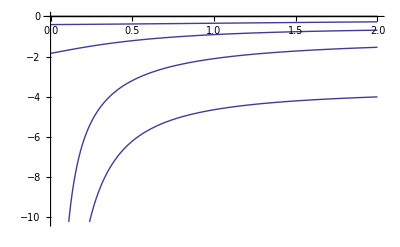

```mathematica
Plot[Sort[Eigenvalues[GG1.GG2[X]]],{X,0,2}]
```

```mathematica
Eigensystem[GG2[2.0].GG1]
```

{{-14.9726,-5.80953,-5.18761,3.64516,2.27379,-0.449197},{{0.117758,-0.620393,-0.774582,0.0282658,-0.0146792,-0.0159443},{0.0102934,-0.0963558,-0.015282,-0.0713369,0.677504,0.725448},{0.0100567,0.97278,-0.145169,0.00211626,0.123232,0.131657},{-0.389662,-0.536137,-0.740588,-0.0850625,-0.0433278,-0.0560119},{0.00663892,0.00691448,0.00834316,-0.0105492,-0.780174,0.625344},{0.124828,0.0657102,-0.00504295,-0.537998,-0.583023,-0.592214}}}

```mathematica
MatrixForm[GG1.GG2[1]]
```

(-1 | 1 | 3/2 | 0 | 0 | 0
1/2 | -1/2 | 0 | 0 | 0 | 0
1/2 | -3/2 | -7/2 | 1 | 0 | 0
0 | 1 | 2 | -2 | 1 | 1
0 | 0 | 0 | 1/2 | -1/2 | -1/2
0 | 0 | 0 | 1/2 | -1/2 | -1/2)

```mathematica
MatrixForm[GG2[1].GG1]
```

(-1 | 1/2 | 1/2 | 0 | 0 | 0
1 | -1/2 | -3/2 | 1 | 0 | 0
3/2 | 0 | -7/2 | 2 | 0 | 0
0 | 0 | 1 | -2 | 1/2 | 1/2
0 | 0 | 0 | 1 | -1/2 | -1/2
0 | 0 | 0 | 1 | -1/2 | -1/2)

```mathematica
MatrixForm[Table[0,{i,2},{j,2}]]
```

```mathematica
H=({{a-c, -a-c-2I b}, {a+c-2I b, c-a}})
```

{{a-c,-a-2 ⅈ b-c},{a-2 ⅈ b+c,-a+c}}

```mathematica
MatrixForm[H^2]
```

((a-c)^2 | (-a-2 ⅈ b-c)^2
(a-2 ⅈ b+c)^2 | (-a+c)^2)

```mathematica
Eigensystem[{{(a-c)^2,(-a-2 ⅈ b-c)^2},{(a-2 ⅈ b+c)^2,(-a+c)^2}}]
```

{{-4 (b^2+a c),2 (a^2+2 b^2+c^2)},{{-(a+2 ⅈ b+c)/(a-2 ⅈ b+c),1},{-(-a-2 ⅈ b-c)/(a-2 ⅈ b+c),1}}}

```mathematica
Eigensystem[H]
```

{{-2 √(-b^2-a c),2 √(-b^2-a c)},{{-(-a+c+2 √(-b^2-a c))/(a-2 ⅈ b+c),1},{-(-a+c-2 √(-b^2-a c))/(a-2 ⅈ b+c),1}}}

```mathematica
HH=({{b, a}, {c, -b}})
```

{{b,a},{c,-b}}

```mathematica
Eigensystem[HH]
```

{{-√(b^2+a c),√(b^2+a c)},{{-(-b+√(b^2+a c))/c,1},{-(-b-√(b^2+a c))/c,1}}}

```mathematica
MatrixForm[HH.HH]
```

(b^2+a c | 0
0 | b^2+a c)

```mathematica
Transpose[GG1.GG2[1]].(GG1.GG2[1])==(GG1.GG2[1]).Transpose[GG1.GG2[1]]
```

False